# -Graphics- TDC Workshop: Inteligência Artificial com Wolfram Language

## Daniel Carvalho - Wolfram Research - dcarvalho@wolfram.com - @danielscarvalho http://www.thedevelopersconference.com.br

## Aprender o básico de Wolfram Language on-line

Elementary Introduction to the Wolfram Langage 2nd ed

-Graphics-

Manipulação de listas

Programação funcional (curso on-line)

Introdução rápida para programadores

## Wolfram Language e Mathematica no Raspberry Pi

Raspberry Pi

## Arquitetura Cliente Servidor

Wolfram Language Scripts

CDF (A grosso modo, um PDF computável)

Mathematica

## Wolfram Cloud

https://www.wolframcloud.com/

WOLFRAM DEVELOPMENT PLATFORM

## Inteligência Artificial

Wolfram Language tem diversas funções que facilitam o uso de Inteligência Artificial em seus projetos.

ImageIdentify[]

TextRecognize[]

Classify[]

Interpreter[]

BarcodeRecognize[]

Predict[]

NetTrain[]

Entrada livre de texto (=, ==, WolframAlpha, Entity)

Análise de DNA

Processamento de Imagens

Morfologia Matemática

Segmentação

Etc

Entre outros...

### Automatic

As diversas funções do Mathematica tomam a decisões para escolher o método mais apropriado e resolver o problema face a entrada de dados, porém o método pode ser especificado pelo programador.

```mathematica
Method-> "NeuralNetwork"
```

Method→NeuralNetwork

## Identificação de Imagens

É possível identificar objetos e o contexto de imagens, e obter detalhes estatísticos da análise
(imagen obtida no Google para uso apenas didático, são de autoria de seus respectivos autores)

```mathematica
(* carro1, carro2, conference, wolf *)
Import["carro1.jpg"]
ImageIdentify[%]
```

```mathematica
Import["carro2.jpg"]
ImageIdentify[%]
```

```mathematica
imgW=Import["wolf.jpg"]
ImageIdentify[imgW]
```

```mathematica
Table[ImageIdentify[imgW, SpecificityGoal -> i], {i, 0, 1, .1}]
WordCloud[%]
```

## Reconhecimento de Texto (OCR)

OCR d’hora!!! 🐺 
(imagen obtida no Google para uso apenas didático)

```mathematica
invoice=-Graphics-;
```

```mathematica
ImageTake[invoice,{1200,-1640},{350,-400}]
TextRecognize[ImageResize[%,Scaled[4]],Language-> "German"]
```

## Classificação - Inteligência Artificial & Estatística

Treinar uma função para realizar classificação
(imagens obtidas no Google para uso didático, são de autoria de suas respectivas marcas)

```mathematica
cerveja =Classify[
<|
"Heineken"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},

"Brahma"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
"Skol"-> {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
|>]
```

```mathematica
cerveja[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
cerveja[{-Graphics-,-Graphics-,-Graphics-},"Probabilities"]
```

## Classificação - Inteligência Artificial & Estatística

Fonte: Exemplos Workshop Wolfram

Classificação de dígitos manuscritos. Utilizando MNIST database banco de dados de digitos manuscritos

```mathematica
digit=Classify[<|
0->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
1->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
3->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
4->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
5->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
6->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
7->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
8->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
9->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

```mathematica
digit[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
digit[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Probabilities"]
```

Classificação de imagens: Noite e Dia!!!

```mathematica
daynight =Classify[<|"Night"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Day"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

```mathematica
daynight[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

## Classificação - Inteligência Artificial & Estatística

Fonte: Etienne Bernard

```mathematica
legendary=Classify[<|
"Griffin"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
"Centaur"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
"Dragon"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
"Unicorn"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

```mathematica
legendary[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

## Predição - Inteligência Artificial & Estatística

```mathematica
nota=Predict[{"E"-> 0, "A"-> 10, "A+" -> 11,"C"-> 5, "B"-> 6, "B"-> 7, "B"-> 8, "D"-> 2}]
```

```mathematica
nota["A"]
```

```mathematica
nota["C"]
```

## Feature Extraction

Fonte: Etienne Bernard

### Search System

```mathematica
dogs={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
fe=FeatureExtraction[dogs]
```

```mathematica
fe[-Graphics-]
```

```mathematica
nf=Nearest[fe[dogs]->Automatic]
```

```mathematica
nearestdog=dogs[[First@nf[fe[#]]]]&
```

```mathematica
nearestdog[-Graphics-]
```

```mathematica
nearestdog[-Graphics-]
```

```mathematica
nearestdog[-Graphics-]
```

## Interpretação Inteligente

Isso é muito LOCO!!! Ctrl =

Testar: MIT, SP, NYC, KM - M, RAD - DEG, Taj Mahal, Esphinge...

FullForm[]
Ctrl + =

```mathematica
GeoGraphics[GeoDisk[LinguisticAssistant, Quantity[1, "Kilometers"]]]
```

```mathematica
Entity["Country","China"][EntityProperty["Country","Population"]]/Entity["Country","Brazil"][EntityProperty["Country","GDP",{"CurrencyUnit"->"CurrentUSDollar"}]]
```

```mathematica
Entity["Country","Brazil"][EntityProperty["Country","Population"]]+ Entity["Country","China"][EntityProperty["Country","Population"]]+ Entity["Country","India"][EntityProperty["Country","Population"]]+ Entity["Country","Russia"][EntityProperty["Country","Population"]]+ Entity["Country","SouthAfrica"][EntityProperty["Country","Population"]]-Entity["Country","World"][EntityProperty["Country","Population"]]
```

```mathematica
UnitConvert[Quantity["100.00", "USDollars"], "BrazilianReais"]
```

```mathematica
Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}][EntityProperty["City","Population"]]/Entity["City",{"Sertaozinho","SaoPaulo","Brazil"}][EntityProperty["City","Population"]]
```

```mathematica
GeoGraphics[GeoDisk[Interpreter["Location"]["23.47°S 46.67°W"],Quantity[1, "Kilometers"]]]
```

```mathematica
Interpreter["Date"]["June 23, 1988"]
```

```mathematica
Interpreter["DateTime"]["Tue 10 Nov 2015 20:55:46 GMT +0"]
```

```mathematica
GeoGraphics[GeoDisk[Interpreter["Location"]["23.47°S 46.67°W"],Quantity[1, "Kilometers"]]]
```

```mathematica
FullForm[Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}]]
```

Entrada de texto livre em inglês (linguagem natural) é feito usando =  no início da célula. Free text input.

WolframAlphaQueryParseResults

Para incluir entidades no código utilize Ctrl + =

```mathematica
Entity["Language","Portuguese"][EntityProperty["Language","Speakers"]]
```

Free-Form & External Input

## Leitura de Código de Barras

Reconhecimento de códigos de barras, inclusive QRCODE
(Imagens obtidas no Google images, uso didático, são de propriedade de seus respectivos autores)

```mathematica
BarcodeRecognize[-Graphics-]
```

```mathematica
BarcodeRecognize[-Graphics-]
```

## Entrada em texto livre

Um dos objetivos do Mathematica é permitir que “não programadores” possam obter seus resultados e programas usando linguagem natural. É um grande desafio!!!

= sertaozinho to sao paulo
= show sky now
= solar system now
= what is the meaning of life?
= who you are?
= who is Sonia Braga?
= apple, google, ibm, oracle

## Processamento de Imagem

Encontrar faces

```mathematica
img=Import["conference.jpg"]
facesList=FindFaces[%]
ImageTrim[img, #] & /@ facesList
```

```mathematica
Show[img, Graphics[{EdgeForm[{Red, Thick}], Opacity[0], Rectangle @@@ facesList}]]
```

Contar objetos em uma imagem

```mathematica
images={ImageTake[-Graphics-,{1,-2}],ImageTake[-Graphics-,{1,-2}]}
```

{-Graphics-,-Graphics-}

```mathematica
Manipulate[
Module[{centroidData,combinedImage,gfImage},
centroidData=ComponentMeasurements[combinedImage=Binarize[gfImage = GaussianFilter[images⟦index⟧,filter]],{"Centroid"}]⟦All,2,1⟧;
Pane[
 Switch[
step,
1,Column[{Text@"Original image",Image[images⟦index⟧,ImageSize-> 400]}],
2,Column[{Text@"Apply a Gaussian filter to reduce image noise.",Image[gfImage,ImageSize-> 400]}],
3,Column[{Text@"Binarize to get only a black-and-white binary image.",Image[combinedImage,ImageSize-> 400]}],
4,Column[{Text@"Center of each cluster",MatrixForm[centroidData]}],
5,Column[{Text@"Result: original image with objects counted.",

Show[Image[images⟦index⟧,ImageSize-> 400],
Graphics[{If[index ==1,White,Black],
Circle[#,8]&/@centroidData,
Red,
Table[Inset[Style[ToString[i],FontSize->15,FontWeight->Bold],centroidData⟦i⟧],
{i,1,Length[centroidData]}]}]]

}]
 ],
ImageSize->{420,350},Alignment->Center]
],

{step,1,5,1,Setter},
{{filter,3,"blurring radius"},1,20,1,Appearance->"Labeled"},
{{index,1,"image"},{1-> "low contrast",2-> "high contrast"}},
SaveDefinitions->True]
```

Counting Objects in Images

## Alinhamento de DNA e Automatos Celulares Smith-Waterman Similarity

Idéia maluca!!  \[FreakedSmiley]

Nucleotídeos: Adenine, Guanine, Thymine, Cytosine

```mathematica
ChemicalData[#,"MoleculePlot"]&/@ EntityClass["Chemical","Nucleotides"]
```

Alinhamento de DNA

```mathematica
SequenceAlignment[
"GTCACC",
"GTCATT"]
```

{GTCA,{CC,TT}}

```mathematica
SequenceAlignment[
"Não é comigo",
"é comigo"]
```

{{Não ,},é comigo}

DNA Similaridade

```mathematica
SmithWatermanSimilarity[
{1,1,1,0,0,0,1},
{1,0,1,0,0,0,2}]
```

4.

Usando algoritmos de DNA para estudar (pesquisar) comportamento de Automatos Celulares

```mathematica
Manipulate[

Module[{ca, recurrence, swsSerie},

(* algoritmos *)
init=RandomInteger[1,size];
ca=CellularAutomaton[rule,init,size-1];
recurrence = Table[SmithWatermanSimilarity[ca1,ca2],{ca1,ca},{ca2,ca}];
swsSerie=SmithWatermanSimilarity[#⟦1⟧,#⟦2⟧]&/@Partition[Riffle[Drop[ca,-1],Rest[ca]],2];

(* visualização *)
Grid[{{
ArrayPlot[ca,Frame-> None,ImageSize-> {100,100}],
ListPlot[swsSerie,Filling->Axis,AxesLabel-> {"steps","sws"},Joined->join, ImageSize-> {200,100}] },
{ArrayPlot[recurrence,Frame-> None,ColorFunction->"Rainbow",ImageSize-> {250,250},PlotLabel-> Text@"Smith-Waterman similarity recurrence plot"],
SpanFromLeft}},Frame-> All,Alignment->{Center,Center}]],

(* manipulate interatividade *)
{{rule,110,"rule number"},0,255,1,Appearance-> "Labeled"},
{{size,50},10,100,1,Appearance-> "Labeled"},
{join,{False,True}}
]
```

Applying the Smith - Waterman Similarity to Cellular Automata

Cellular Automata

SmithWatermanSimilarity

## Grupamento

### ClusterClassify

Fonte: Etienne Bernard

```mathematica
eruptions = ExampleData[{"Statistics","OldFaithful"}]
```

```mathematica
ListPlot[eruptions,FrameLabel->{"Eruption time in minutes","Waiting time to next eruption in minutes"},Frame->True]
```

```mathematica
c=ClusterClassify[eruptions]
```

```mathematica
clusters = GatherBy[eruptions, c];
ListPlot[clusters,FrameLabel->{"Eruption time in minutes","Waiting time to next eruption in minutes"},Frame->True]
```

## Regressão

```mathematica
ListLinePlot[Table[Sin[x]+x*.1,{x,0,100}]]
```

```mathematica
data= Table[{x,Sin[x]+x*.1},{x,0,100}]
```

```mathematica
lm=LinearModelFit[data,x,x]
```

```mathematica
lm[10]
```

```mathematica
data⟦11⟧
```

```mathematica
Show[ListPlot[data, ColorFunction->Hue],Plot[lm[x],{x,0,100}],Frame->True]
```

```mathematica
ListPlot[Table[Sin[x]+x^2,{x,0,100}]]
```

```mathematica
data= Table[{x,Sin[x]+x^2},{x,0,100}]
```

```mathematica
lm=LinearModelFit[data,x,x]
```

```mathematica
Show[ListPlot[data, ColorFunction->Hue],Plot[lm[x],{x,0,100}],Frame->True]
```

## FindFormula

Encontra uma função generalizada com base nos dados

{{-10,75},{-9,59},{-8,45},{-7,33},{-6,23},{-5,15},{-4,9},{-3,5},{-2,3},{-1,3},{0,5},{1,9},{2,15},{3,23},{4,33},{5,45},{6,59},{7,75},{8,93},{9,113},{10,135}}

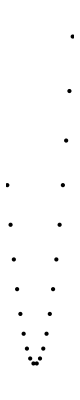

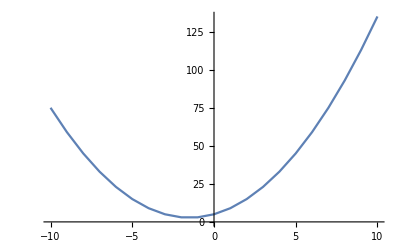

```mathematica
data = Table[{x, 3+x^2+3x+2},{x,-10,10}]
Graphics[Point[#]&/@ data]
ListLinePlot[data]
```

```mathematica
FindFormula[data,coisa]
```

Piecewise[{{5.+3. coisa+1. coisa^2, -10.≤coisa<10.}, {0, True}}]

```mathematica
data = Table[{x,10*Sin[x]+Cos[x]*2},{x,-50,50}]
Graphics[Point[#]&/@ data]
ListLinePlot[data]
```

```mathematica
FindFormula[data,x]
```

```mathematica
data = Table[{x,N[10*Cos[x+Sin[x]]]},{x,1,50}]
Graphics[Point[#]&/@ data]
ListLinePlot[data]
```

```mathematica
FindFormula[data,x]
```

```mathematica
ListLinePlot[Table[10. Cos[Abs[x]+Sin[x]],{x,1,50}]]
```

## Implemente suas próprias funções de IA

```mathematica
net=LinearLayer[];
trained=NetTrain[net,{1->1.9,2->4.1,3->6.0,4->8.1}]
```

```mathematica
trained[2.5]
```

```mathematica
ListPlot[Table[x^2+3x+2, {x,0,20}]]
```

```mathematica
values=Table[x^2+3x+2, {x,0,20}]
```

```mathematica
data=Rule[#[[1]],#[[2]]]&/@Partition[Riffle[Range[Length[values]],values],2]
```

```mathematica
FullForm[1->2]
```

```mathematica
trainedPar=NetTrain[net,data]
```

```mathematica
trainedPar[10]
```

```mathematica
ListPlot[Table[trainedPar[a],{a,0,20,1}]]
```

Para saber mais:

Machine Learning

Neural Networks

## Mais sobre a Wolfram, Mathematica e Wolfram Language

New Kind of Science

Wolfram Science Summer School

Wolfram Alpha

Demonstration Project